h = 0.05,  x ∈ [1., 1.5] 
{y' (x) =(x^2 (y(x))^2 -  (2 x + 1) y(x) + 1.)/x, 
{y (1.) = 0.)
 Контрольные вопросы : 2, 5, 9

```mathematica
ClearAll["y*"]
rt=NDSolve[{y'[x]==(x^2 y[x]^2-(2 x+1) y[x]+1.)/x,y[1.]==0.},y,{x,1.,1.5}]
yt[x_]:=y[x]/.rt[[1]];
```

{{y→InterpolatingFunction[…]}}

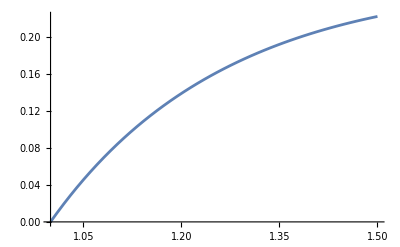

```mathematica
g1=Plot[yt[x],{x,1.,1.5}]
```

```mathematica
f[x_,y_]:=(x^2 y^2-(2 x+1) y+1.)/x;
```

```mathematica
h=0.1;
a=1.;
b=1.5;
x0=a;
y0=0.;
X={x0};
yE={y0};
maxI = 1000;
iter = 0;
While[x0<b && iter < maxI,x1=x0+h;
y1 = y0 + h f[x0, y0];
yp = y0 + h/2 f[x0, y0];
yh2 = yp + h/2 f[x0 + h/2, yp];
R = Abs[(y1 - yh2)/7]; 
Print[" x = ",x1," y = ",y1, " R = ", R];
AppendTo[X,x1];
AppendTo[yE,y1];
x0=x1;
y0=y1;
iter++;
];
```

x = 1.1 y = 0.1 R = 0.00137581

x = 1.2 y = 0.162918 R = 0.000835524

x = 1.3 y = 0.203276 R = 0.000531067

x = 1.4 y = 0.229279 R = 0.000349302

x = 1.5 y = 0.245835 R = 0.000235825

{{1.,0.},{1.1,0.1},{1.2,0.162918},{1.3,0.203276},{1.4,0.229279},{1.5,0.245835}}

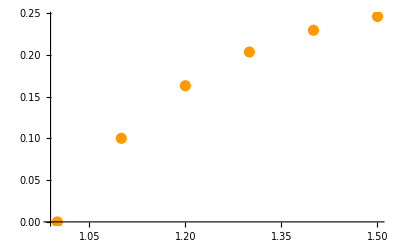

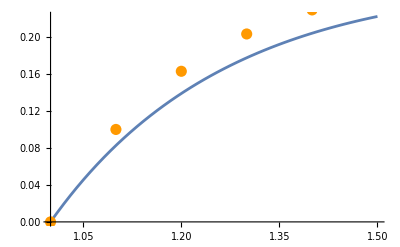

```mathematica
ynum=Transpose[{X,yE}]
g2=ListPlot[ynum,PlotStyle->{Hue[0.1],PointSize[0.02]}]
Show[g1,g2]
```

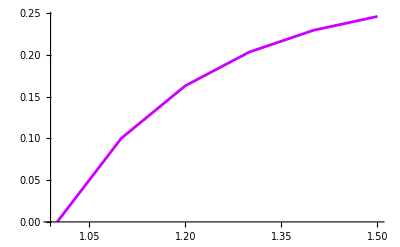

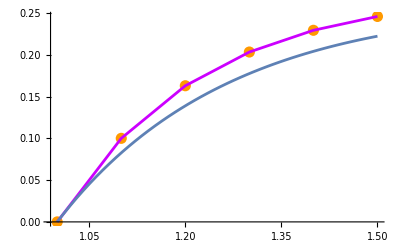

```mathematica
g3=ListPlot[ynum,Joined->True,PlotStyle->{Hue[0.8],PointSize[0.02]}] (*Ломанная Эйлера*)
Show[g2,g3,g1]
```

-Graphics-

```mathematica
f[x_,y_] := (x^2 y^2-(2 x+1) y+1.)/x;
```

```mathematica
h=0.1;
a=1.;
b=1.5;
x0=a;
y0=0.;
X=List[x0];
yR=List[y0];
maxI = 10000;
iter = 0;
While[x0<b && iter < maxI,x1=x0+h;
 k1=h * f[ x0 , y0 ];
     k2=h  f[ x0+ h/3 , y0+ k1/3 ];  
k3 = h f[x0 + 2/3 h, y0 + 2/3 k2];
     y1 = y0 +k1/4 + 3/4 k3;

kh1 = h/2 f[x0, y0];
kh2 = h/2 f[x0 + h/6, y0 + k1/3];
kh3 = h/2 f[x0 + 1/3 h, y0 + 2/3 k2];
yh2 = y0 + kh1/4 + 3/4 kh3;
R = Abs[(y1-yh2)/7];
Print[" x = ",x1," y = ",y1, " R = ", R];

AppendTo[X,x1];
AppendTo[yR,y1];
x0=x1;
y0=y1;
iter++;
];
```

x = 1.1 y = 1.05107 R = 0.144086

x = 1.2 y = -0.160315 R = 0.166771

x = 1.3 y = 1.02289 R = 0.161031

x = 1.4 y = -0.139878 R = 0.161296

x = 1.5 y = 0.870185 R = 0.137444

{{1.,0.},{1.1,1.05107},{1.2,-0.160315},{1.3,1.02289},{1.4,-0.139878},{1.5,0.870185}}

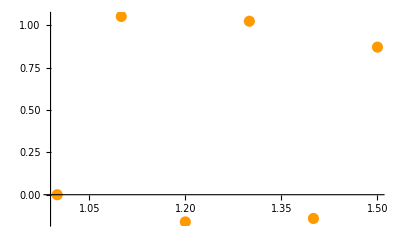

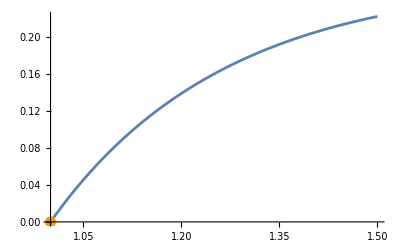

```mathematica
ynum=Transpose[{X,yR}]
g2=ListPlot[ynum,PlotStyle->{Hue[0.1],PointSize[0.02]}]
Show[g1,g2]
```

```mathematica
h=0.1;

b=1.5;
x0=1.;
y0=0.;
n=(b-x0)/h+1;
xA=Table [t,{t,x0,b,h}];
yA=Table[0,{n}] ;
yA[[1]]=yR[[1]];
yA[[2]]=yR[[2]];
yA[[3]]=yR[[3]];

fa = Table[0, {n}];
For[i=3, i<n, i++,
fa[[i-2]] = f[ xA[[i-2]],yA[[i-2]]] ;
fa[[i-1]] = f[ xA[[i-1]],yA[[i-1]] ];
fa[[i]] = f[ xA[[i]],yA[[i]] ];

yA[[i+1]]=yA[[i]]+h/12*(23*fa[[i]]-16*fa[[i-1]]+5*fa[[i-2]]);	

fa[[i+1]] = f[xA[[i+1]], yA[[i+1]]];
Print[yA];
yA[[i+1]]=yA[[i]]+h/12*(5 * fa[[i+1]]+8*fa[[i]]-fa[[i-1]]);

fa[[i+1]] = f[xA[[i+1]], yA[[i+1]]];
]
```

{0.,1.05107,-0.160315,0.258491,0,0}

{0.,1.05107,-0.160315,-0.0587993,-0.0939693,0}

{0.,1.05107,-0.160315,-0.0587993,0.0335554,0.083365}

```mathematica
ynumAdams = Transpose[{xA, yA}];
```

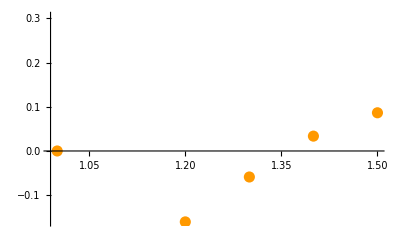

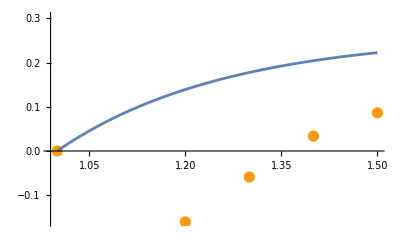

```mathematica
g2Adams=ListPlot[ynumAdams , PlotStyle->{Hue[0.1] , PointSize[0.02]} ] 
Show[g2Adams, g1]
```